# Solve the differential equation: 1. (x+2)dy-(2y)dx=0 Solution: (x+2)dy-(2Y)dx => ⅆy/ⅆx=(2y)/(x+2) => y’ =(2y)/(x+2)

```mathematica
ClearAll["Global`*"]
```

```mathematica
DSolve[y'[x]==(2y[x])/(x+2),y[x],x]
```

{{y[x]→(2+x)^2 C[1]}}

## 2. Plot the solutions for C[1]=-2,-1,0,1,2

```mathematica
ClearAll["Global *"]
```

```mathematica
y[x] = (2+x)^2 c1
```

c1 (2+x)^2

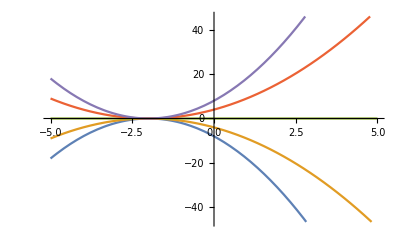

```mathematica
Plot[Evaluate[Table[y[x],{c1,-2,2}]],{x,-5,5}]
```

## 3. Solve y’’+9y’=0,y’[0]=0,y[2]=1, Plot the solution.

```mathematica
ClearAll["Global`*"]
```

```mathematica
sol1=DSolve[{y''[x] + 9y'[x]==0,y'[0]==4,y[2]==1},y[x],x]
```

{{y[x]→1/9 ⅇ^(-18-9 x) (-4 ⅇ^18+4 ⅇ^(9 x)+9 ⅇ^(18+9 x))}}

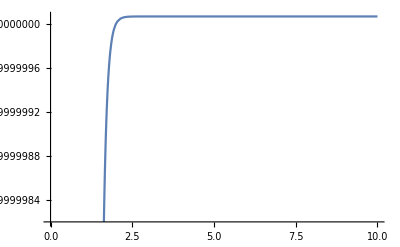

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {DSolve[{9 y'[0.204286]+y''[0.204286]==0,True,True},y,0.204286]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of DSolve::dsvar will be suppressed during this calculation.

DSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{9. y'[0.000204286]+y''[0.000204286]==0.,True,True},y,0.000204286]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {DSolve[{9 y'[0.000204286]+y''[0.000204286]==0,True,True},y,0.000204286]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

DSolve::dsvar: 0.000204286 cannot be used as a variable.

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {9 y'[x]+y''[x]==0,True,True}.

Syntax::bktmop: Expression "sol1=DSolve{(y''[x])+(9y'[x])==0,y'[0]==4,y[2]==1},y,x]" has no opening "[".

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::naqs: -4+y'[0]==0&&-1+y[2]==0/.DSolve`DSolveFirstOrderODEDump`LinearFirstOrderODE[c1 (2+x)^2,0,-9,1]==0 is not a quantified system of equations and inequalities.

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

```mathematica
Plot[y[x]/.sol1,{x,0,10}]
```

## 4. Plot the numerical solution of y''+9y'=0,y'[0]=0,y[2]=1

```mathematica
sol2 = NDSolve[{y''[x]+9y'[x]==0,y'[0]==4,y[2]==1},y,{x,0,10}]
```

{{y→InterpolatingFunction[…]}}

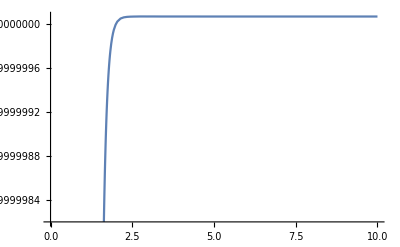

```mathematica
Plot[y[x]/.sol2,{x,0,10}]
```

#### Forced harmonic oscillator: (ⅆ^2 y)/(ⅆ t^2)+pⅆy/ⅆt+qy=cos(ωt) We can split this equation into a system: ⅆy/ⅆt=v, ⅆv/ⅆt=-qy-pv+cos(ωt)

```mathematica
ClearAll["Global`*"]
```

```mathematica
sol3=DSolve[{y'[t]==v[t],v'[t]==-2y[t]+Cos[1.56t],y[0]==0,v[0]==0},{y,v},t]
```

{{v→Function[{t},(-2.79346×10^-16+7.99207×10^-16 ⅈ) Cos[1.41421 t]+(2.93744×10^-16-8.40401×10^-16 ⅈ) Cos[0.145786 t] Cos[1.41421 t]-(1.43984×10^-17-4.11938×10^-17 ⅈ) Cos[1.41421 t] Cos[2.97421 t]+(3.42967-9.51926×10^-17 ⅈ) Cos[1.41421 t] Sin[0.145786 t]-(3.26156+1.28024×10^-16 ⅈ) Sin[1.41421 t]+(3.42967+1.34623×10^-16 ⅈ) Cos[0.145786 t] Sin[1.41421 t]-(0.168112+6.59877×10^-18 ⅈ) Cos[2.97421 t] Sin[1.41421 t]-(6.97612×10^-16-8.40401×10^-16 ⅈ) Sin[0.145786 t] Sin[1.41421 t]+(0.168112-4.66604×10^-18 ⅈ) Cos[1.41421 t] Sin[2.97421 t]-(3.41947×10^-17-4.11938×10^-17 ⅈ) Sin[1.41421 t] Sin[2.97421 t]],y→Function[{t},(-2.42515-1.00967×10^-16 ⅈ) ((-0.950983+5.08256×10^-33 ⅈ) Cos[1.41421 t]+(1.+0. ⅈ) Cos[0.145786 t] Cos[1.41421 t]-(0.0490168+3.1766×10^-34 ⅈ) Cos[1.41421 t] Cos[2.97421 t]-(1.57009×10^-16-1.57009×10^-16 ⅈ) Cos[1.41421 t] Sin[0.145786 t]+(2.63951×10^-17-2.11161×10^-16 ⅈ) Sin[1.41421 t]-(2.77556×10^-17-2.22045×10^-16 ⅈ) Cos[0.145786 t] Sin[1.41421 t]+(1.36049×10^-18-1.08839×10^-17 ⅈ) Cos[2.97421 t] Sin[1.41421 t]-(1.-5.55112×10^-17 ⅈ) Sin[0.145786 t] Sin[1.41421 t]-(7.69609×10^-18-7.69609×10^-18 ⅈ) Cos[1.41421 t] Sin[2.97421 t]-(0.0490168-2.72098×10^-18 ⅈ) Sin[1.41421 t] Sin[2.97421 t])]}}

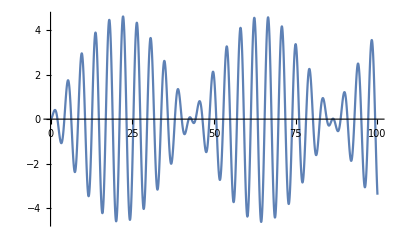

```mathematica
Plot[y[t]/.sol3,{t,0,100}]
```

```mathematica
sol03=DSolve[{y'[t]==v[t],v'[t]==-2y[t]+Cos[156/100 t],y[0]==0,v[0]==0},{y,v},t]
```

{{v→Function[{t},25/542 (-50 √2 Sin[√2 t]+39 Cos[(-39/25+√2) t] Sin[√2 t]+25 √2 Cos[(-39/25+√2) t] Sin[√2 t]-39 Cos[(39/25+√2) t] Sin[√2 t]+25 √2 Cos[(39/25+√2) t] Sin[√2 t]-39 Cos[√2 t] Sin[(-39/25+√2) t]-25 √2 Cos[√2 t] Sin[(-39/25+√2) t]+39 Cos[√2 t] Sin[(39/25+√2) t]-25 √2 Cos[√2 t] Sin[(39/25+√2) t])],y→Function[{t},-1/1084 25 (-100 Cos[√2 t]+50 Cos[√2 t] Cos[(-39/25+√2) t]+39 √2 Cos[√2 t] Cos[(-39/25+√2) t]+50 Cos[√2 t] Cos[(39/25+√2) t]-39 √2 Cos[√2 t] Cos[(39/25+√2) t]+50 Sin[√2 t] Sin[(-39/25+√2) t]+39 √2 Sin[√2 t] Sin[(-39/25+√2) t]+50 Sin[√2 t] Sin[(39/25+√2) t]-39 √2 Sin[√2 t] Sin[(39/25+√2) t])]}}

```mathematica
sol4=NDSolve[{y'[t]==v[t],v'[t]==-2y[t]+Cos[1.56t],y[0]==0,v[0]==0},{y,v},{t,0,100}]
```

{{y→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

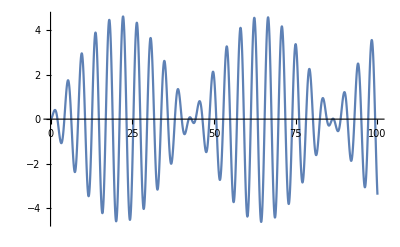

NDSolve::ndnl: Endpoint Null in {t,100.,Null} is not a real number.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{9 y'[0.204286]+y''[0.204286]==0,True,True},y,{0.204286,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{9. y'[0.000204286]+y''[0.000204286]==0.,True,True},y,{0.000204286,0.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{9 y'[0.000204286]+y''[0.000204286]==0,True,True},y,{0.000204286,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Plot[y[t]/.sol4,{t,0,100}]
```